# The Sandpile Model

Jonas Kaufman & Jon Ueki

## Introduction

The Sandpile Model, also known as the Bak-Tang-Wiesenfeld model is a cellular automaton that aims to model systems that display critical, self-organizing behavior.

## Graphics Setup

```mathematica
Module[{cmds= {"Plot", "ListPlot", "ListLinePlot", "ListLogPlot", "ListLogLogPlot","LogPlot","LogLogPlot","ListStepPlot"}},
For[j=1, j≤ Length[cmds],j++,SetOptions[Symbol[ cmds[[j]] ], Frame->True,LabelStyle->{Larger, FontFamily->"Utopia"}]]
]
```

## 1-D Model

The model takes place on a row representing half a sandpile where each cell has a slope z_n and height h_n where z_n=h_n-h_(n+1).

```mathematica
length=20;
zCrit1D=1;
```

```mathematica
randomRow[]:=row=Table[RandomInteger[zCrit],{length}]
constantRow[c_]:=row=Table[c,{length}]
```

Adding a grain at cell n corresponds to  z_n  -> z_n + 1 and z_(n-1)  -> z_(n-1) - 1

```mathematica
addGrain[] :=Module[{r},
r=RandomInteger[{1,length}];
row[[r]]++;
If[r>1,row[[r-1]]--]
];
```

If the slope at any cell exceeds the critical slope z_c, then the cell “topples,” sending a grain of sand to the next cell. This corresponds to z_n  -> z_n - 2 and z_(n±1)  -> z_(n±1) + 1

```mathematica
relaxation1D[]:=Module[{i,stable=False},
While[!stable,
stable=True;
For[i=1,i≤ length,i++,
If[row[[i]]> zCrit1D,
stable=False;
If[1<i<length,row[[i]]-=2;row[[i+1]]++;row[[i-1]]++;];
If[i==1,row[[i]]-=2;row[[i+1]]++;];
If[i==length,row[[i]]--;row[[i-1]]++];
];
];
];
]
```

```mathematica
pourSand[numGrains_]:=Module[{n,rows={}},
For[n=1,n≤numGrains,n++,
addGrain[];
relaxation1D[];
AppendTo[rows,row]; 
];
rows
]
```

If sand is added randomly to an empty row, the pile eventually reaches a critical state in which the slope at each cell is simply the critical slope.

```mathematica
constantRow[0];
rows=pourSand[600];
Animate[GraphicsColumn[{
ListStepPlot[Table[Total[rows[[t]][[i;;]]],{i,length}],FrameLabel->{"i","h"},PlotRange->{0,length*zCrit1D+1}],
ListStepPlot[rows[[t]],FrameLabel->{"i","z"},PlotRange->{-zCrit1D-1,zCrit1D+1}]
}],{t,1,Length[rows],1,Appearance->"Labeled"},AnimationRunning->False,AnimationRate->Automatic]
```

## 2-D Model

In two dimensions, the model takes place on a grid representing a quarter of a sandpile where each cell has a slope z_(i,j) .

#### Initialization

```mathematica
gridSize = 25; (*how many rows and columns in a grid*)
zCrit = 3; (*The max slope possible*)
grid = Table[Table[0, {n, gridSize}], {n, gridSize}]; (*the sandpile*)
avalancheFreq = Table[0, {n, 2 * gridSize^2}]; (*how many times an avalanche of a certain size occurs*)
avalancheTime = {}; (*The size of an avalanche when the nth grain of sand is dropped*)
```

#### Updating Code

We are using nonconservative perturbations in which a grain is added by simply increasing the slope at a cell by one.

```mathematica
addSand[random_,place_] :=Module[{i, j}, 
If[random,(*If we activate random, then add grains randomly*)
i=RandomInteger[{1,gridSize}];j=RandomInteger[{1,gridSize}];,
i=place[[1]];j=place[[2]];
];
grid[[i,j]]+=2;
(*If[j≠1,grid[[i,j-1]]--];
If[i≠1,grid[[i-1,j]]--];*)
update[i,j];
];
```

In 2D, a toppled cell loses 4 from its slope and sends 1 slope to each of its compass neighbors.

```mathematica
update[i_,j_]:=Module[{},(*updates the cell according to these set of rules*)
If[grid[[i,j]]>zCrit,
s++;grid[[i,j]]-=4;
(* add sand to neighbors *)
If[i≠1,grid[[i-1,j]]++];
If[j≠1,grid[[i,j-1]]++];
If[i≠gridSize,grid[[i+1,j]]++];If[j≠gridSize,grid[[i,j+1]]++];
(* relax neighbors *)
If[i≠1,update[i-1,j]];
If[j≠1,update[i,j-1]];
If[i≠gridSize,update[i+1,j]];If[j≠gridSize,update[i,j+1]];
];
]
```

This funcion drops totalSand_ many grains of sand and updates the sandpile

```mathematica
run[totalSand_, random_:False,place_:{1,1}] := Module[{n,T,sList={},TList={}},
For[n=1,n≤ totalSand,n++,
s=0;
addSand[random,place];
AppendTo[sList,s];
AppendTo[avalancheTime, s];
avalancheFreq[[s+1]]++;
];
sList
]
```

#### Initialize the Grid with random slopes or constant slopes

```mathematica
randomGrid[]:=grid = Table[Table[RandomInteger[zCrit], {n, gridSize}], {n, gridSize}];
```

```mathematica
constantGrid[c_]:=grid = Table[Table[c, {n, gridSize}], {n, gridSize}];
```

#### Visualization Functions

Distribution of slopes

```mathematica
slopeDist[]:= Module[{slopes, slopedist = {}, i, j},
slopes = Table[0, {n, 0, zCrit}];
For[i=1, i≤ gridSize, i++,
For[j=1, j≤gridSize,j++,
slopes[[grid[[i,j]] + 1]]++;
];
];
(*make x-coordinate and y-coordinate pair *)
For[i=1, i≤Length[slopes], i++,
AppendTo[slopedist, {i-1, slopes[[i]]}];
];
slopedist
]
```

Visualize the height of the sandpile

```mathematica
heights[grid_]:=Module[{i,j,heights=Table[Table[0, {n, 2*gridSize}], {n, 2*gridSize}]},
For[i=gridSize-1,i≥0,i--,
For[j=gridSize-1,j≥0,j--,
heights[[i + gridSize,j + gridSize]]=If[i==0 || j==0, 
0.5 (grid[[i+1,j+1]] + heights[[i+1 + gridSize,j + gridSize]]+heights[[i + gridSize,j+1 + gridSize]]),0.5(grid[[i,j]]+heights[[i+1 + gridSize,j + gridSize]]+heights[[i + gridSize,j+1 + gridSize]])];

heights[[gridSize-i, gridSize+j]] = heights[[i + gridSize,j + gridSize]];
heights[[gridSize+i, gridSize - j]] = heights[[i + gridSize,j + gridSize]];
heights[[gridSize-i, gridSize - j]] = heights[[i + gridSize,j + gridSize]];
];
];
heights
]
```

#### Run and Plot the Simulation

```mathematica
constantGrid[0];
```

```mathematica
run[10000, True];
```

Part::partw: Part 1544 of {4365,4101,63,557,536,83,170,90,124,119,31,60,36,37,32,30,35,21,23,27,18,21,25,9,8,18,12,17,16,7,8,13,11,11,7,9,5,6,10,7,8,6,5,8,6,5,9,6,5,5,«1200»} does not exist.

Set::partw: Part 1544 of avalancheFreq⟦s+1⟧ does not exist.

Part::partw: Part 1544 of {4365,4101,63,557,536,83,170,90,124,119,31,60,36,37,32,30,35,21,23,27,18,21,25,9,8,18,12,17,16,7,8,13,11,11,7,9,5,6,10,7,8,6,5,8,6,5,9,6,5,5,«1200»} does not exist.

Part::partw: Part 1275 of {6637,4984,563,849,778,267,316,216,241,217,128,153,121,108,102,107,109,76,73,90,82,63,76,52,41,50,56,56,55,42,43,55,46,46,34,40,34,36,35,35,34,30,26,32,29,27,34,21,28,23,«1200»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::partw: Part 1275 of avalancheFreq⟦s+1⟧ does not exist.

```mathematica
Dynamic[ArrayPlot[grid,PlotLegends->Automatic]]
```

```mathematica
ListPlot3D[heights[grid],InterpolationOrder->1, Mesh->None,ColorFunction->"Rainbow",ViewPoint->{2,0, 1}]
```

-Graphics3D-

```mathematica
Manipulate[ListPlot[avalancheTime, PlotRange-> {{Max[0, xmax- 100], xmax}, {0,100}},Filling -> Axis, AxesLabel->{HoldForm[Time],HoldForm[Avalanche Size]},PlotLabel->HoldForm[Avalanche Size vs Time],LabelStyle->{GrayLevel[0],Bold}], {xmax, 100, Length[avalancheTime]}]
```

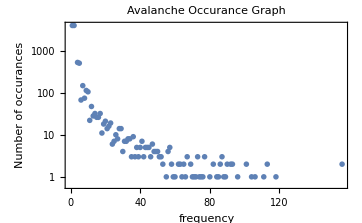

```mathematica
Show[ListLogPlot[avalancheFreq],AxesLabel->{HoldForm[frequency],HoldForm[Number of occurances]},PlotLabel->HoldForm[Avalanche Occurance Graph],LabelStyle->{14,GrayLevel[0]}]
```